```mathematica
{{data = Import["E:\\Alessio\\Desktop\\Computazionale\\es12\\data.txt","Table"]}, {}}
```

{{{{0,-1.06677,0.502834},{1,-0.537969,0.943306},{2,0.81077,0.910453},{3,0.343251,0.235019},{4,0.289061,0.327385},{5,-1.02706,0.288321},99988,{49994,-0.184044,-0.550291},{49995,-0.452824,-0.866596},{49996,-1.49205,-0.343823},{49997,-1.08588,-1.31217},{49998,-0.815251,-0.138084},{49999,0.429861,-0.315216}}},{Null}}
 |  |  |  |

```mathematica
f= Transpose[Take[data][[All, {2}]]]
g = Transpose[Take[data][[All, {3}]]]
```

{{-1.06677,-0.537969,0.81077,0.343251,0.289061,-1.02706,-0.8653,0.018783,-1.19135,0.690161,-0.73839,0.555415,-0.882142,-0.438598,-0.533201,0.231753,-0.443352,99966,-1.38554,-0.623033,1.07766,-1.61356,0.543667,-0.731863,-0.899133,-0.328984,0.367075,0.036178,0.001402,-0.184044,-0.452824,-1.49205,-1.08588,-0.815251,0.429861}}
 |  |  |  |

{{0.502834,0.943306,0.910453,0.235019,0.327385,0.288321,0.030035,0.809641,0.79741,1.08525,1.03233,0.495506,0.929395,0.33916,0.254411,0.552995,0.228585,99966,-0.251794,-0.231633,-1.9271,-0.479131,-0.739531,-0.567174,-0.227301,-1.74021,-0.410518,-0.957726,-0.091955,-0.550291,-0.866596,-0.343823,-1.31217,-0.138084,-0.315216}}
 |  |  |  |

(ⅇ^(-x^2))/(√π)

1

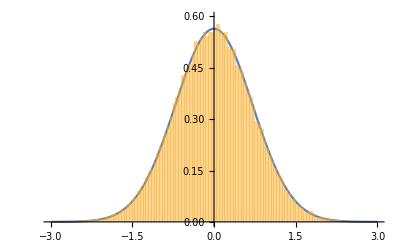

```mathematica
f1 = Exp[-x^2]/Sqrt[Pi] 
Integrate[f1, {x,-Infinity,Infinity}]
Show[Plot[f1,{x,-3,3}, PlotRange->{0,0.6}],Histogram[f, 100,"PDF"]]
```

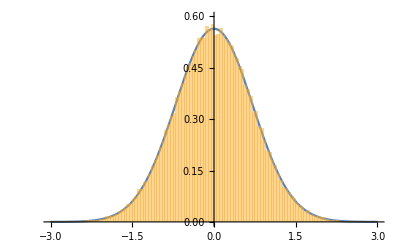

```mathematica
Show[Plot[f1,{x,-3,3}, PlotRange->{0,0.6}],Histogram[g, 100,"PDF"]]
```

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}]
```

√π

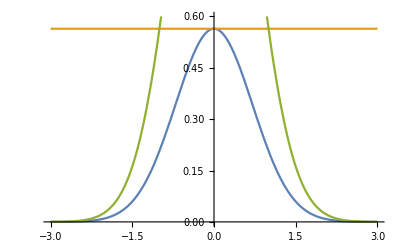

```mathematica
Plot[{f1,1/Sqrt[Pi],Exp[1-x^2]/Sqrt[Pi]},{x,-3,3}, PlotRange->{0,0.6}]
```